```mathematica
(* EP 2
Parte 1: Calcular a seguinte função
f[x_]:=1-(12G)/π^2∫_0^1 p^2/(√(p^2+x^2))ⅆp;
   Escolhendo G=2 temos:*)
```

```mathematica
f[x_]:=1-24/π^2∫_0^1 p^2/(√(p^2+x^2))ⅆp;
```

```mathematica
dx=0.001 ;
```

```mathematica
x = Table[i,{i,0,1,dx}];
```

```mathematica
(*Cálculo da função pelo Método dos Trapézios*)
```

```mathematica
At = 1/2 Sum[(f[x[[i]]]+f[x[[i+1]]]) dx,{i,1,Length[x]-1}] //N
```

0.0696336

```mathematica
(*Parte 2: Plotando o gtráfico*)
```

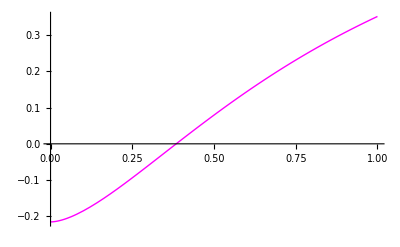

```mathematica
Plot[f[x],{x,0,1},PlotStyle->{Magenta,Thick}]
```

```mathematica
(*Parte 3: Cálculo da Raíz*)
```

```mathematica
ϵ=1.×10^-6;
a=3.×10^-1; b=5.×10^-1;
isRoot=False;j=0;
```

```mathematica
While[
isRoot==False,
	x=(a+b)/2.;
	j++;
	Print[j,"  ",x,"  ",f[x]];
	isRoot = Abs[f[x]]≤ϵ;
	If[f[a]×f[x]<0, b=x,a=x]
]
```

1  0.4  0.0109318

2  0.35  -0.0242078

3  0.375  -0.00660051

4  0.3875  0.00217824

5  0.38125  -0.00220837

6  0.384375  -0.0000143233

7  0.385938  0.00108215

8  0.385156  0.00053396

9  0.384766  0.00025983

10  0.38457  0.000122756

11  0.384473  0.0000542173

12  0.384424  0.0000199472

13  0.384399  2.81202×10^-6

14  0.384387  -5.75561×10^-6

15  0.384393  -1.47179×10^-6

16  0.384396  6.70112×10^-7